```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\qwqwh\Documents\GitHub\UILC

Get::noopen: Cannot open ./src/uic.wl.

Import::nffil: File ./src/uic.wl not found during Import.

```mathematica
<< "./src/UIC.wl"
```

```mathematica
GeneralizedLambertian[1,1,Pi/6,1]
```

(√3)/2

```mathematica
ESCCoefficientLinear[7,80.7]
```

0.134784

```mathematica
ESCCoefficientRectangular[7,7,50]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.172011

```mathematica
f[x_,n_,m_,s_]:= Sum[Power[((n+1-2*i)^2+(m+1-2*j)^2)*(x^2/4)+1, -(s+6)/2] *(1-((s+3)*(n+1-2*i)^2-(m+1-2*j)^2)*(x^2/4)),{j,m},{i,n}];
```

```mathematica
x/.FindRoot[f[x,7,7,50],{x,0.5}]
```

FindRoot::nlnum: The function value {7. Null} is not a list of numbers with dimensions {1} at {x} = {0.5}.

ReplaceAll::reps: {FindRoot[f[x,7,7,50],{x,0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.FindRoot[f[x,7,7,50],{x,0.5}]

```mathematica
x/.FindMinimum[{f[x,7,7,50],0<= x<= 1},{x,0.5}][[2]]
```

0.172011

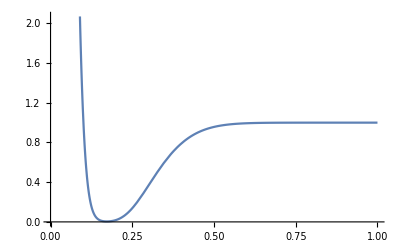

```mathematica
Plot[f[x,7,7,50],{x, 0,1}]
```

```mathematica
f[0.6,7,7,50]
```

7 Null

```mathematica
LamberFindde[2,0.1,1]
```

General::ivar: 1 is not a valid variable.

General::ivar: 1. is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

FindRoot::nlnum: The function value {∂_1. 0.} is not a list of numbers with dimensions {1} at {UIC`Private`d} = {0.5}.

ReplaceAll::reps: {FindRoot[∂_(UIC`Private`d,1) 2,{UIC`Private`d,2/4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

UIC`Private`x/.{UIC`Private`x,0.5}/.FindRoot[∂_(UIC`Private`d,1) 2,{UIC`Private`d,2/4}]

```mathematica
1.11
```

1.11

```mathematica
LamberD[2,0.2,1.11]
```

-1.1685

```mathematica
Plot[LamberDi[1,x,0.1,0.2,1.11], {x, -0.1,1.1}]
```

General::ivar: -0.999755 is not a valid variable.

General::ivar: -0.754857 is not a valid variable.

General::ivar: -0.509959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
I0=1
h=0.5
w=1
s=1.11
x=0.2
```

1

0.5

1

1.11

0.2

```mathematica
LamberDi[I0,x,h,w,s]
```

General::ivar: 0.4 is not a valid variable.

4. ∂_(0.4,1.11) 2.

```mathematica
I0/h^2 *LamberD[w/h,x/h,s]
```

-3.13154

```mathematica
N[LamberFinddmApprox[80]]
```

0.130575

```mathematica
LamberFindde[2,0.5,1.11]
```

General::ivar: 1.11 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

FindRoot::nlnum: The function value {∂_1.11 0.} is not a list of numbers with dimensions {1} at {UIC`Private`d} = {0.5}.

ReplaceAll::reps: {FindRoot[∂_(UIC`Private`d,1.11) 2,{UIC`Private`d,2/4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

UIC`Private`x/.{UIC`Private`x,0.5}/.FindRoot[∂_(UIC`Private`d,1.11) 2,{UIC`Private`d,2/4}]